```mathematica
loadNotebook["inz_off_6_model.nb"];
```

```mathematica
wyliczSterowanie[h_,hd_,k1_,k2_]:=(
tmp=Transpose[G2.Transpose[{η[t]}]][[1]];
z = {tmp[[1]], tmp[[2]], tmp[[6]]};
Z=D[z,t] /. {D[ϕ[t],t]->Subscript[η, 1][t],D[θ[t],t]->Subscript[η, 2][t]};
Kdd={Coefficient[Z,D[Subscript[η, 1][t],t]],Coefficient[Z,D[Subscript[η, 2][t],t]],Coefficient[Z,D[Subscript[η, 3][t],t]]} // Transpose;
P =Z-Kdd.{D[Subscript[η, 1][t],t],D[Subscript[η, 2][t],t],D[Subscript[η, 3][t],t]};
(*Kdd// Simplify // MatrixForm // Print;
Det[Kdd]//Simplify // Print;
Inverse[Kdd] // Simplify // MatrixForm // Print;
P // Simplify // MatrixForm // Print;*)
K1 = k1*IdentityMatrix[3];
K2 = k2*IdentityMatrix[3];
sterowanie=Inverse[Kdd].(-P+D[D[hd,t],t]-K1.(D[h,t]-D[hd,t])-K2.(h-hd));
sterowanie
);

rozwiazRownania[sterowanie_,q0_,tmax_]:=(
pstrona = Transpose[G2.Transpose[{η[t]}]][[1]];
lstrona = D[q[t],t];
lstrona = Join[lstrona,D[η[t],t]];
pstrona = Join[pstrona, sterowanie];
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
tosolve = (rownanie /.{l-> 0.1, R-> 0.03}) ~Join~ q0;
rozwiazanie = NDSolve[tosolve, {x,y, Subscript[θ, 0],ϕ, θ,ψ, Subscript[η, 1],Subscript[η, 2],Subscript[η, 3]}, {t,0,tmax}, Method->Automatic, MaxSteps->1000000];
rozwiazanie
);

wyrysuj[rozwiazanie_, tmax_,anim_,i_]:=Module[{},
loc="C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\";

plot1=Plot[{x[t]-xd[t]/.rozwiazanie,y[t]-yd[t]/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_x","e_y"},{0.90,0.75}],PlotRange->{-0.1,0.1}, PlotStyle->{Thick}];
plot1//Print;
Export[loc<>"inz_off_6_lin_dyn_"<>ToString[i]<>"_1.pdf",plot1];

plot2=Plot[wirowanie*t-ψ[t]/.rozwiazanie,{t,0,tmax},AxesLabel->{"t","e_ψ"},PlotRange->{-0.1,0.1}, PlotStyle->{Thick}];
plot2//Print;
Export[loc<>"inz_off_6_lin_dyn_"<>ToString[i]<>"_2.pdf",plot2];

zoomStart=12;
range=0.05;
xyMinMax={{zoomStart-range,zoomStart+range},{-30,30}};
g=Graphics[{EdgeForm[Thick],White,Disk[],Inset[Plot[Evaluate[{Subscript[η, 1][t]} /.rozwiazanie],{t,zoomStart-range,zoomStart+range},Axes->{True,False},ImageSize->140,Ticks->{{zoomStart-range,zoomStart,zoomStart+range},{-1,1}}]]},ImageSize->150];
plot3=Plot[Evaluate[{Subscript[η, 1][t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η_1"},Axes->{True, True},Epilog->{Inset[g,{40,0.5}]}];
plot3//Print;
Export[loc<>"inz_off_6_lin_dyn_"<>ToString[i]<>"_3.pdf",plot3];

plot4=Plot[Evaluate[{Subscript[η, 2][t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η_2"},Axes->{True, True}];
plot4//Print;
Export[loc<>"inz_off_6_lin_dyn_"<>ToString[i]<>"_4.pdf",plot4];

plot5=Plot[Evaluate[{ϕ[t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ϕ"},Axes->{True, True}];
plot5//Print;
Export[loc<>"inz_off_6_lin_dyn_"<>ToString[i]<>"_5.pdf",plot5];

plot6=Plot[Evaluate[{θ[t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","θ"},Axes->{True, True}];
plot6//Print;
Export[loc<>"inz_off_6_lin_dyn_"<>ToString[i]<>"_6.pdf",plot6];

plot7=Plot[Evaluate[{ψ'[t]} /.rozwiazanie], {t,0,tmax}, PlotRange->{195,205}, AxesLabel->{"t","ψ̇"},Axes->{True, True}];
plot7//Print;
Export[loc<>"inz_off_6_lin_dyn_"<>ToString[i]<>"_7.pdf",plot7];

krzywa1[t_] = {x[t] ,y[t]} /. rozwiazanie;

p1[t_] = ((Agms[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x1[t_] = (p1[t])[[1,1,1]];
y1[t_] = (p1[t])[[1,2,1]];
krzywas[t_] = {x1[t], y1[t]} /. rozwiazanie;

p2[t_] = ((Agm2[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x2[t_] = (p2[t])[[1,1, 1]];
y2[t_] = (p2[t])[[1,2, 1]];
krzywa2[t_] = {x2[t], y2[t]}/. rozwiazanie;

ẋ[t_] = (x1'[t] /.rozwiazanie)[[1]];
ẏ[t_] = (y1'[t] /. rozwiazanie)[[1]];
v[t_] = Re[Sqrt[(ẋ[t])^2+(ẏ[t])^2]];

krzywad[t_]={xd[t],yd[t]};

a1 = Animate[
Show[
{Plot[v[t], {t, 0, tmax}, PlotRange->All,AxesLabel->{"t","v"}]},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{t,v[t]}]]}]
}
],{t,0,tmax}];

curvs = ParametricPlot[{krzywas[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->{Red}, Axes->{True, True}, AxesOrigin->{0,0}];
curv1 = ParametricPlot[{krzywa1[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Blue}, Axes->{True, True},AxesOrigin->{0,0}];
curv2 = ParametricPlot[{krzywa2[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Yellow}, Axes->{True, True}, AxesOrigin->{0,0}];
curvd = ParametricPlot[{krzywad[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Black}, Axes->{True, True}, AxesOrigin->{0,0}];
plot8=ParametricPlot[{krzywa1[t],krzywad[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0}];
plot8//Print;
Export[loc<>"inz_off_6_lin_dyn_"<>ToString[i]<>"_8.pdf",plot8];


p11[t_]=Evaluate[{x[t],y[t]}/.rozwiazanie];
p22[t_]=Evaluate[{x2[t],y2[t]}/.rozwiazanie];
x11[t_]=(x[t]/.rozwiazanie)[[1]];
y11[t_]=(y[t]/.rozwiazanie)[[1]];
x22[t_]=(x2[t]/.rozwiazanie)[[1]];
y22[t_]=(y2[t]/.rozwiazanie)[[1]];
a2=Animate[
Show[
{curvs,curv1,curv2,curvd},
{
Graphics[{PointSize[0.03],Red,Point[Dynamic[p11[t]]]}],
Graphics[{PointSize[0.03], Red,Point[Dynamic[p22[t]]]}],
Graphics[{PointSize[0.02], Black,Point[Dynamic[{xd[t],yd[t]}]]}],
Graphics[
{Thickness[0.002],Green,
Line[
{
Dynamic[{x11[t],y11[t]}],
Dynamic[{x2[t],y2[t]}]
}
]
}]
}
],{t,0,tmax}];
If[anim,Print[a1],0];
If[anim,Print[a2],0];
0
];
```

```mathematica
Det[Kdd]//Simplify
```

R^2 Cos[ϕ[t]]

0

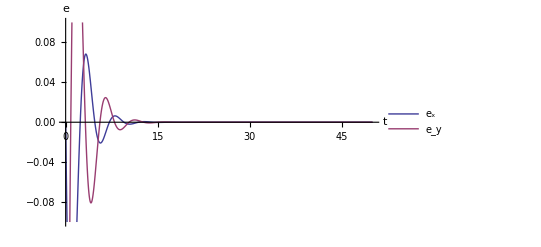

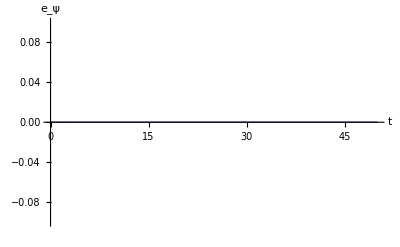

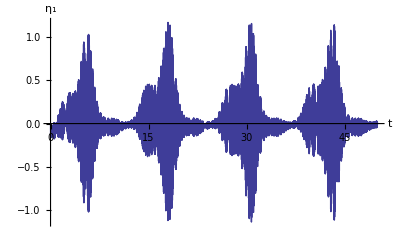

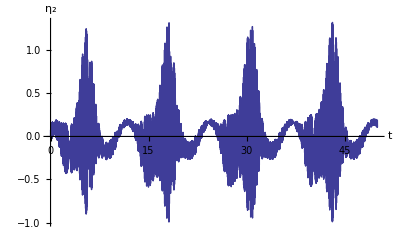

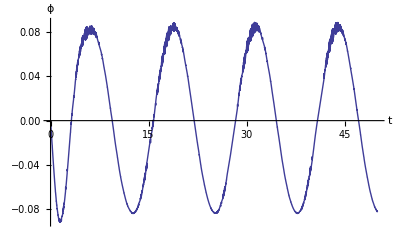

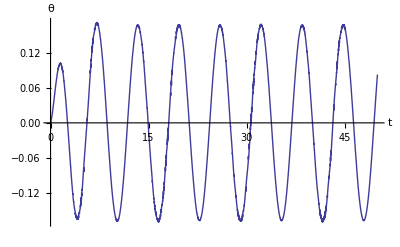

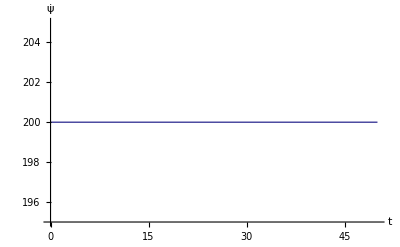

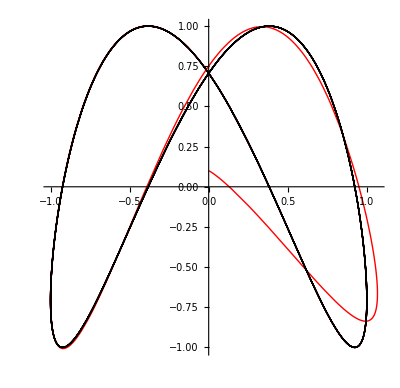

```mathematica
h={x[t],y[t],ψ[t]};
wirowanie = 200;
tmax=50;
q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0, ϕ[0]==0, θ[0]==0, ψ[0]==0, Subscript[η, 1][0]==0,Subscript[η, 2][0]==0, Subscript[η, 3][0]==wirowanie};


For[i=0,i<1,i++,
Print[i];
Which[i==0,{xd[t_],yd[t_]}=osemka[t,1],i==1,{xd[t_],yd[t_]}=kolo[t,3,1],i==2,{xd[t_],yd[t_]}=liniaX[t,3,1],True,{xd[t_],yd[t_]}=kwadrat[t,3,10]];
hd={xd[t],yd[t],wirowanie*t};
sterowanie=wyliczSterowanie[h,hd,1,2];
rozwiazanie = rozwiazRownania[sterowanie,q0,tmax];
wyrysuj[rozwiazanie, tmax,False,i];
];
```

```mathematica
Kdd//Simplify//MatrixForm
```

(0 | R Cos[ϕ[t]] | -R Cos[θ[t]] Sin[ϕ[t]]
-R | 0 | -R Sin[θ[t]]
0 | 0 | 1)

```mathematica
P//Simplify//MatrixForm
```

(-R (-Sin[θ[t]] Sin[ϕ[t]] η_2[t] η_3[t]+η_1[t] (Sin[ϕ[t]] η_2[t]+Cos[θ[t]] Cos[ϕ[t]] η_3[t]))
-R Cos[θ[t]] η_2[t] η_3[t]
0)